```mathematica
(*Преобразование кватерниона в матрицу вращения*)
quat2Mat[qu_]:={{1-2*qu[[3]]^2-2*qu[[4]]^2,2*(qu[[2]]*qu[[3]]+qu[[1]]*qu[[4]]),2*(qu[[2]]*qu[[4]]-qu[[1]]*qu[[3]])},{2*(qu[[2]]*qu[[3]]-qu[[1]]*qu[[4]]),(1-2*qu[[2]]^2-2*qu[[4]]^2),2*(qu[[3]]*qu[[4]]+qu[[1]]*qu[[2]])},{2*(qu[[2]]*qu[[4]]+qu[[1]]*qu[[3]]),2*(qu[[3]]*qu[[4]]-qu[[1]]*qu[[2]]),(1-2*qu[[2]]^2-2*qu[[3]]^2)}};

(*Функция вращения вектора с помощью кватерниона*)
rotateWithQuaternion=
{(#1[[1]]*(1-2*#2[[3]]^2-2*#2[[4]]^2)+#1[[2]]*2*(#2[[2]]*#2[[3]]+#2[[1]]*#2[[4]])+#1[[3]]*2*(#2[[2]]*#2[[4]]-#2[[1]]*#2[[3]])),
(#1[[1]]*2*(#2[[2]]*#2[[3]]-#2[[1]]*#2[[4]])+#1[[2]]*(1-2*#2[[2]]^2-2*#2[[4]]^2)+#1[[3]]*2*(#2[[3]]*#2[[4]]+#2[[1]]*#2[[2]])),
(#1[[1]]*2*(#2[[2]]*#2[[4]]+#2[[1]]*#2[[3]])+#1[[2]]*2*(#2[[3]]*#2[[4]]-#2[[1]]*#2[[2]])+#1[[3]]*(1-2*#2[[2]]^2-2*#2[[3]]^2))}&;

(*Вершины тетраэдра с заданным радиусом описанной сферы*)
tetraPoint1={#*Sqrt[8]/3,0,#*(-1/3)}&;
tetraPoint2={#*(-Sqrt[2]/3),#*Sqrt[2/3],#*(-1/3)}&;
tetraPoint3={#*(-Sqrt[2]/3),#*(-Sqrt[2/3]),#*(-1/3)}&;
tetraPoint4={0,0,#}&;

(*Радиус рабочего органа меньше радиуса сферы в k раз*)
r = R*k;

(*Координаты центра тяжести рабочего органа*)
Ic={x,y,z};

(*Координаты сферических шарниров (O) и универсальных шарниров (I) несмещенного рабочего органа*)
O1=tetraPoint1[R];O2=tetraPoint2[R];O3=tetraPoint3[R];O4=tetraPoint4[R];
I1`o=tetraPoint1[r];I2`o=tetraPoint2[r];I3`o=tetraPoint3[r];I4`o=tetraPoint4[r];

(*Кватернин вращения на угол theta относительно оси, заданной сферическими координатами alpha и omega*)
q={Cos[theta],Sin[theta]*Cos[alpha]*Cos[omega],Sin[theta]*Sin[alpha]*Cos[omega],Sin[theta]*Sin[omega]};

(*Координаты универсальных шарниров смещенного рабочего органа*)
I1=Ic+rotateWithQuaternion[I1`o,q];
I2=Ic+rotateWithQuaternion[I2`o,q];
I3=Ic+rotateWithQuaternion[I3`o,q];
I4=Ic+rotateWithQuaternion[I4`o,q];

(*Система уравнений прямой и обратной кинематической задачи осесимметричного способа ограничения степеней подвижности рабочего органа*)
lhs`sym={
SquaredEuclideanDistance[O1,I1]-L1^2,
SquaredEuclideanDistance[O2,I2]-L2^2,
SquaredEuclideanDistance[O3,I3]-L3^2,
Dot[(O1-I1),(I2-I3)],
Dot[(O2-I2),(I1-I3)],
Dot[(O3-I3),(I2-I1)]
};
equations`sym=Thread[lhs`sym=={0,0,0,0,0,0}];

(*Система уравнений прямой и обратной кинематической задачи зеркальносимметричного способа ограничения степеней подвижности рабочего органа*)
lhs`asym={
SquaredEuclideanDistance[O1,I1]-L1^2,
SquaredEuclideanDistance[O2,I2]-L2^2,
SquaredEuclideanDistance[O3,I3]-L3^2,
Dot[(O1-I1),(I2-I3)],
Dot[(O4-I4),(I1-I3)],
Dot[(O4-I4),(I2-I1)]
};
equations`asym=Thread[lhs`asym=={0,0,0,0,0,0}];

(*Неизвестные величины обратной кинематической задачи*)
variables={L1,L2,L3,theta,alpha,omega};
```

```mathematica
(*Текущая рассматриваемая задача*)
equations=equations`asym;

(*Конкретные значения параметров и координат сферических шарниров*)
parameters={R->1,k->1/3};
{O1`v,O2`v,O3`v,O4`v}={O1,O2,O3,O4}/.parameters;

(*Начальные приближения численного решения*)
L0=(R-r)/.parameters;
eps=0.001;
initialConditions`inverse={{L1,L0},{L2,L0},{L3,L0},{theta,eps},{alpha,eps},{omega,eps}};
initialConditions`forward={{x,#[[1]]},{y,#[[2]]},{z,#[[3]]}}&;

(*Сетка положений центра тяжести*)
delta=0.04;
maxvalue=(R-r)/.parameters;
maxvalue=Floor[maxvalue/delta]*delta;
range=Range[-maxvalue,maxvalue,delta];

(*Шарообразная область*)
grid=Select[Tuples[range,3],(Norm[#]<=(R-r)/.parameters)&];

(*Численное решение обратной кинематической задачи в области*)
calculator=FindRoot[#1/.Join[parameters,#2],#3,MaxIterations->100]&;

xyz={x->#[[1]],y->#[[2]],z->#[[3]]}&;
solutions=AssociationMap[calculator[equations,xyz[#],initialConditions`inverse]&,grid];

(*Численное решение прямой кинематической задачи в области для контроля точности решения обратной кинематической задачи*)
positions=AssociationMap[calculator[equations[[{1,2,3}]],solutions[#],initialConditions`forward[#]]&,grid];

(*Максимальная ошибка решения на сетке*)
error=Norm[Values[positions[#]]-#]/.parameters&;
sortedErrors=Sort[error/@grid,#1>#2&]

(*Таблицы координат универсальных шарниров*)
I1`v=AssociationMap[I1/.Join[parameters,xyz[#],solutions[#]]&,grid];
I2`v=AssociationMap[I2/.Join[parameters,xyz[#],solutions[#]]&,grid];
I3`v=AssociationMap[I3/.Join[parameters,xyz[#],solutions[#]]&,grid];
I4`v=AssociationMap[I4/.Join[parameters,xyz[#],solutions[#]]&,grid];

(*Длина четвертой опоры*)
L4=AssociationMap[Sqrt[SquaredEuclideanDistance[O4`v,I4`v[#]]]&,grid];
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot::lstol will be suppressed during this calculation.

FindRoot::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot::lstol will be suppressed during this calculation.

{0.311706,1.71098×10^-12,1.06214×10^-12,1.02567×10^-12,7.48446×10^-13,6.13477×10^-13,5.69028×10^-13,3.21472×10^-13,3.12341×10^-13,2.7472×10^-13,2.71804×10^-13,2.11427×10^-13,2.11193×10^-13,2.0657×10^-13,2.04552×10^-13,2.03015×10^-13,1.76157×10^-13,1.70646×10^-13,1.68546×10^-13,1.55037×10^-13,1.34451×10^-13,1.19519×10^-13,1.14679×10^-13,1.09302×10^-13,1.05147×10^-13,1.01336×10^-13,9.71006×10^-14,9.58437×10^-14,9.50938×10^-14,8.99388×10^-14,8.83742×10^-14,8.51006×10^-14,7.76316×10^-14,19315,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}
 |  |  |  |

```mathematica
(*Расчет максимального угла поворота в шарнирах для каждого положения*)
maximumAngleUniversal=Pi;
maximumAngleSpherical=Pi/2;
positionMaxJointsAngles=AssociationMap[{Max[VectorAngle[O1`v-I1`v[#],I1`v[#]-#],VectorAngle[O2`v-I2`v[#],I2`v[#]-#],VectorAngle[O3`v-I3`v[#],I3`v[#]-#],VectorAngle[O4`v-I4`v[#],I4`v[#]-#]],Max[VectorAngle[O1`v-I1`v[#],O1`v],VectorAngle[O2`v-I2`v[#],O2`v],VectorAngle[O3`v-I3`v[#],O3`v],VectorAngle[O4`v-I4`v[#],O4`v]]}&,grid];

(*Расчет минимальной и максимальной длин опор*)
minimumLegLength=(1/2)*(R-r)/.parameters;
maximumLegLength=3*minimumLegLength;
positionMinMaxLegsLengths=AssociationMap[{Min[Lookup[solutions[#],L1],Lookup[solutions[#],L2],Lookup[solutions[#],L3],L4[#]],Max[Lookup[solutions[#],L1],Lookup[solutions[#],L2],Lookup[solutions[#],L3],L4[#]]}&,grid];

(*Определение допустимости положения*)
positionAdmissibility=AssociationMap[((positionMaxJointsAngles[#][[1]]<maximumAngleUniversal)&&(positionMaxJointsAngles[#][[2]]<maximumAngleSpherical)&&(positionMinMaxLegsLengths[#][[1]]>=minimumLegLength)&&(positionMinMaxLegsLengths[#][[2]]<=maximumLegLength))&,grid];
```

Max::nord: Invalid comparison with 3.14159-2.10734×10^-8 ⅈ attempted.

General::stop: Further output of Max::nord will be suppressed during this calculation.

Less::nord2: Comparison of Max[2.59578,3.14159-2.10734×10^-8 ⅈ] and π is invalid.

Less::nord2: Comparison of Max[2.92322,3.14159-2.10734×10^-8 ⅈ] and π is invalid.

Less::nord2: Comparison of Max[2.56524,3.14159-2.10734×10^-8 ⅈ] and π is invalid.

General::stop: Further output of Less::nord2 will be suppressed during this calculation.

```mathematica
(*Изображение полной рабочей зоны*)
nearestpoint=Nearest[Select[Keys[positionAdmissibility],(positionAdmissibility[#]&&(Norm[#]<=(R-r-delta)/.parameters))&]];
inRegion[pt:{_Real,_Real,_Real},eps_Real]:=TrueQ[SquaredEuclideanDistance[nearestpoint[pt,1][[1]],pt]<eps^2];
Show[{RegionPlot3D[inRegion[{x,y,z},delta],{x,-maxvalue,maxvalue},{y,-maxvalue,maxvalue},{z,-maxvalue,maxvalue},Mesh->False,PlotPoints->40],Graphics3D[{Opacity[0.5],Sphere[{0,0,0},R/.parameters]}]},SphericalRegion->True,PlotRange->All,BoxRatios->Automatic]

(*Расчет максимального радиуса шарообразной области рабочей зоны*)
working`radius=Norm[Nearest[Select[Keys[positionAdmissibility],Not[positionAdmissibility[#]]&],{0,0,0}]]

(*Изображение максимальной шарообразной рабочей зоны*)
Show[{Graphics3D[{Yellow,Opacity[1],Sphere[{0,0,0},working`radius]}],Graphics3D[{Opacity[0.5],Sphere[{0,0,0},R/.parameters]}]},SphericalRegion->True,PlotRange->All,BoxRatios->Automatic]
```

-Graphics3D-

0.339411

-Graphics3D-

```mathematica
(*Интерактивная демонстрация положения рабочего органа*)
line={Thick,Line[#]}&;

Dynamic@updatedVxyz
Dynamic@updatedVadmissibility
Manipulate[
updatedVxyz={{x,y,z},Norm[{x,y,z}]};
updatedVadmissibility={positionAdmissibility[{x,y,z}],positionMaxJointsAngles[{x,y,z}]/Pi*180,positionMinMaxLegsLengths[{x,y,z}]};
If[Norm[{x,y,z}]≤(R-r)/.parameters,
{I1`vv,I2`vv,I3`vv,I4`vv}={I1`v[{x,y,z}],I2`v[{x,y,z}],I3`v[{x,y,z}],I4`v[{x,y,z}]};
Show[{ListPointPlot3D[{{I1`vv,I2`vv,I3`vv,I4`vv},{O1`v,O2`v,O3`v,O4`v}},PlotStyle->{{Red,PointSize[Large]},{Green,PointSize[Large]}}],Graphics3D[line/@{{O2`v,I2`vv},{O3`v,I3`vv},{I1`vv,I2`vv},{I1`vv,I3`vv},{I1`vv,I4`vv},{I2`vv,I3`vv},{I2`vv,I4`vv},{I3`vv,I4`vv}}],
Graphics3D[{Thick,Red,Line[{O1`v,I1`vv}]}],Graphics3D[{Thick,Yellow,Line[{O4`v,I4`vv}]}]},SphericalRegion->True,PlotRange->All,BoxRatios->Automatic],updatedVadmissibility={}],{{x,0.},range},{{y,0.},range},{{z,0.},range},ControlType->Slider]
```

0.170367

{{0,1.6713},{9.80916,0}}

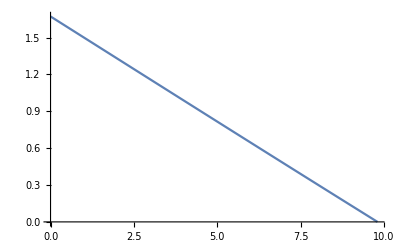

```mathematica
(*Максимальное отклонение центра тяжести робота-сферы*)
g=9.81; (*м/с^2*)
propToSphereRelativeMass=20; (*кг/кг*)
CG=working`radius*(propToSphereRelativeMass/(propToSphereRelativeMass+1)); (*м*)
N[CG]

(*Максимальный угол уклона поверхности*)
maxRamp=N[(ArcSin[CG/R]/Pi*180)/.parameters];

(*Максимальное ускорение в зависимости от уклона поверхности*)
acceleration=((CG-R*Sin[phi*Pi/180])*g/R)/.parameters;(*м/с^2*)

{{0,acceleration/.phi->0},{maxRamp,0}}
Plot[acceleration,{phi,0,maxRamp}]
```